{{0.,1},{0.1,1.1},{0.2,1.2095},{0.3,1.32845},{0.4,1.4568},{0.5,1.59447},{0.6,1.74142},{0.7,1.89756},{0.8,2.06282},{0.9,2.2371},{1.,2.42031}}

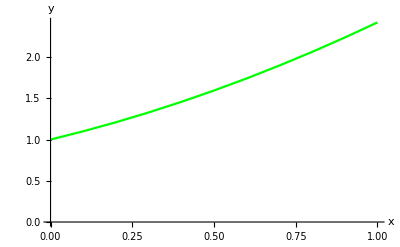

```mathematica
(*Euler's Method*)
h=.1;(*step size or delta x*)
upperbound=1;(* x value want to iterate to*)
iter=upperbound/h;(*the number of iterations*)
x0=0;(*inital condition for x coord*)
x[k_]=x0+k*h;(*function that creates the x coord*)
y[x0]=1;(*intial condition for y coord*)
Do[y[n+1]=y[n]+h*(y[n]-(x[n]^2)/2),{n,0,iter}]; (*loops using Euler's formula to create data*)
data=Table[{x[i],y[i]},{i,0,iter}](*loop pulls data from y pairs with x data*)
Euler=ListPlot[data,PlotStyle->Green,PlotJoined->True,AxesLabel->{"x","y"}]
```